# Boats Boats Goats Goats

## Inputs and Example Plot

5000

{0,0}

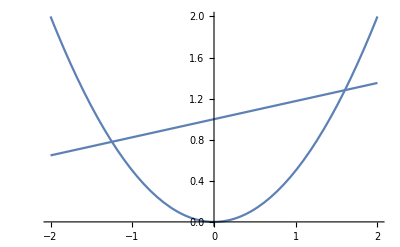

```mathematica
BoatCurve = x^2/2;
HeelAngle = 10;      (*degrees*)
BoatDensity = 300; (*kg/m^3*)
MassBalast = 5000   (*kg*)
COBallast = {0,0}


Show[Plot[BoatCurve, {x,-2,2}],Plot[Tan[HeelAngle Degree]*x+1, {x, -2,2}]]
```

## Calculating Buoyancy point

{0,32/35}

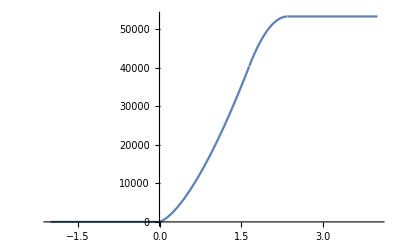

{0.176327,0.660202}

-Graphics-

```mathematica
boat = ImplicitRegion[BoatCurve<y<2&&-2<x<2&&0<y<2,{x,y}];
water = ImplicitRegion[y<Tan[HeelAngle Degree]*x+d&&-2<x<2&&-2<y<4,{x,y}];
under = RegionIntersection[boat,water];

mass = 10*Integrate[BoatDensity,{x,y}∈boat]+MassBalast;
disp = 10*Integrate[1000,{x,y}∈under,Assumptions->{-2<d<4}];
com = 1/mass*(Integrate[BoatDensity*{x,y},{z, 0 ,10}, {x, -2, 2},{y, BoatCurve, 2}]+MassBalast*COBallast)

Plot[disp,{d,-2,4}]
waterline = Solve[disp==mass,d,Reals];
draft = N[d/.waterline[[1]]];

cob = 10*Integrate[1000*{x,y},{x,y}∈under, Assumptions->{-2<d<4}]/disp;
cob/.{d->draft}

Show[RegionPlot[{water/.{d->draft},boat,under/.{d->draft}},AspectRatio->Automatic],ListPlot[{cob/.{d->draft}, com}]]
```

## Calculating Torque and AVS

```mathematica
cob
```

{Piecewise[{{2000/3 (2 d Tan[10 °] √(2 d+Tan[10 °]^2)+Tan[10 °]^3 √(2 d+Tan[10 °]^2)), -1/2 Tan[10 °]^2<d≤2-2 Tan[10 °]}, {500/3 (-2-6 d Cot[10 °]^2+12 Cot[10 °]^4-3 d^2 Cot[10 °]^4-8 Cot[10 °]^6+12 d Cot[10 °]^6-6 d^2 Cot[10 °]^6+d^3 Cot[10 °]^6+2 √(1+2 d Cot[10 °]^2)+4 d Cot[10 °]^2 √(1+2 d Cot[10 °]^2)) Tan[10 °]^4, 2-2 Tan[10 °]<d<2||2≤d<2 (1+Tan[10 °])}, {1000 (4-(-2+d)^2 Cot[10 °]^2+1/8 (-16+(-2+d)^4 Cot[10 °]^4)), d==2 (1+Tan[10 °])}, {0, True}}]/Piecewise[{{2000/3 (2 d √(2 d+Tan[10 °]^2)+Tan[10 °]^2 √(2 d+Tan[10 °]^2)), -1/2 Tan[10 °]^2<d≤2-2 Tan[10 °]}, {-500/3 (2+6 d Cot[10 °]^2-16 Cot[10 °]^3+12 Cot[10 °]^4-12 d Cot[10 °]^4+3 d^2 Cot[10 °]^4-2 √(1+2 d Cot[10 °]^2)-4 d Cot[10 °]^2 √(1+2 d Cot[10 °]^2)) Tan[10 °]^3, 2-2 Tan[10 °]<d<2||2≤d<2 (1+Tan[10 °])}, {1000 (2 (2+(-2+d) Cot[10 °])+1/6 (-8-(-2+d)^3 Cot[10 °]^3)), d==2 (1+Tan[10 °])}, {16000/3, d>2 (1+Tan[10 °])}, {0, True}}],Piecewise[{{400/3 (6 d^2 √(2 d+Tan[10 °]^2)+11 d Tan[10 °]^2 √(2 d+Tan[10 °]^2)+4 Tan[10 °]^4 √(2 d+Tan[10 °]^2)), -1/2 Tan[10 °]^2<d≤2-2 Tan[10 °]}, {-100/3 (8+30 d Cot[10 °]^2+30 d^2 Cot[10 °]^4-96 Cot[10 °]^5+80 Cot[10 °]^6-60 d Cot[10 °]^6+5 d^3 Cot[10 °]^6-8 √(1+2 d Cot[10 °]^2)-22 d Cot[10 °]^2 √(1+2 d Cot[10 °]^2)-12 d^2 Cot[10 °]^4 √(1+2 d Cot[10 °]^2)) Tan[10 °]^5, 2-2 Tan[10 °]<d<2||2≤d<2 (1+Tan[10 °])}, {500 (4 (2+(-2+d) Cot[10 °])+1/20 (-32-(-2+d)^5 Cot[10 °]^5)), d==2 (1+Tan[10 °])}, {6400, d>2 (1+Tan[10 °])}, {0, True}}]/Piecewise[{{2000/3 (2 d √(2 d+Tan[10 °]^2)+Tan[10 °]^2 √(2 d+Tan[10 °]^2)), -1/2 Tan[10 °]^2<d≤2-2 Tan[10 °]}, {-500/3 (2+6 d Cot[10 °]^2-16 Cot[10 °]^3+12 Cot[10 °]^4-12 d Cot[10 °]^4+3 d^2 Cot[10 °]^4-2 √(1+2 d Cot[10 °]^2)-4 d Cot[10 °]^2 √(1+2 d Cot[10 °]^2)) Tan[10 °]^3, 2-2 Tan[10 °]<d<2||2≤d<2 (1+Tan[10 °])}, {1000 (2 (2+(-2+d) Cot[10 °])+1/6 (-8-(-2+d)^3 Cot[10 °]^3)), d==2 (1+Tan[10 °])}, {16000/3, d>2 (1+Tan[10 °])}, {0, True}}]}